### The defining function of the 3n+1 algorithm

```mathematica
(*the function ulam computes one step of the 3k+1 algorithm to a number n*)
ulam[n_]:=If[Mod[n,2]==0 ,n/2,3n+1]


(*the function f allows us to define n as a number not a variable*)
f[n_]:=n
(*the function ulamlist generates a rough list of the ulam procedure to 1*)
```

```mathematica
(*ulamlist[n_]:=Module[{y},y=f[n];While[y>1,
Print[y];y=ulam[y]]]*)
(*the function ulamslist returns a string/list of the numbers in the ulams procedure*)
ulamslist[n_]:=Catch[Module[{y,g},y:=f[n];g:={};While[y>0,
AppendTo[g,y];If[y==1,Throw[g]];y=ulam[y]]]]
(*ulamnumber as defined here, is the number of steps needed in the 3k+1 algorithm to reach 1 plus 1, since the initial number n is included in the list*)
ulamnumber[n_]:=Length[ulamslist[n]]
ulamslistmod8[n_]:=Module[{},
lst=ulamslist[n];
index=ulamnumber[n];
For[i=1,i<index+1,i=i+1,
valu= Part[lst,i];Part[lst,i]=Mod[valu,8]];(*Use Part, as here, to reassign values!*)
Return[lst];];(*While[ k<index+1,valu= Part[lst,k];ReplacePart[lst,k->Mod[valu,8]]];
Return[lst];]*)(*valu= Extract[lst,i]*)(*valu= Part[lst,i],nu=Mod[Valu,8],ReplacePart[i->nu][lst]*)
ulamslistmod8[5]
ulamslist[5]
ulamslistmod8[7]
ulamslist[7]
ulamnumber[4]
ulamnumber[10]
ulamslist[10]
```

{5,0,0,4,2,1}

{5,16,8,4,2,1}

{7,6,3,2,1,4,2,5,0,4,2,5,0,0,4,2,1}

{7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

3

7

{10,5,16,8,4,2,1}

### The sum of steps needed when viewed as a path

```mathematica
(*This gives the sum of the steps taken if we view this as a path from (0,1) to (sumofsteps,1)*)
```

```mathematica
ulamsumdifferences[n_]:=Module[{},
lst=ulamslist[n];
m=ulamnumber[n];
sum=f[n]-1;
For [i =1,i< m,i=i+1,
sum=sum+Abs[(lst[[i+1]]-lst[[i]])]];
Return[sum];]
```

```mathematica
ulamsumdifferences[5]
```

30

```mathematica
ulamsumdifferences[3]
```

40

```mathematica
ulamsumdifferences[7]
```

234

```mathematica
ulamsumdifferences[9]
```

276

### Alternative method for generating the ulam sequence in the mod 8 form

```mathematica
realpartcomplexn[n_]:=Ceiling[n/8]*Cos[Mod[n,8]*Pi/4]
(*The imaginary part is written without the I factor, so it is a real number*)
imagpartcomplexn[n_]:=Ceiling[n/8]*Sin[Mod[n,8]*Pi/4]
```

```mathematica
realpartcomplexn[ulamslist[3]]

imagpartcomplexn[ulamslist[3]]
```

{-1/(√2),0,-1/(√2),2,1,-1,0,1/(√2)}

{1/(√2),2,-1/(√2),0,0,0,1,1/(√2)}

```mathematica
(*Here we define functions that create the x and y coordinates of the pseudo complex numbers corresponding to the list of numbers in ulamslist for a number n*)
tablereal[n_]:=realpartcomplexn[ulamslist[n]]
tableimag[n_]:=imagpartcomplexn[ulamslist[n]]
```

```mathematica
X:=tablereal[10]
Y:=tableimag[10]
```

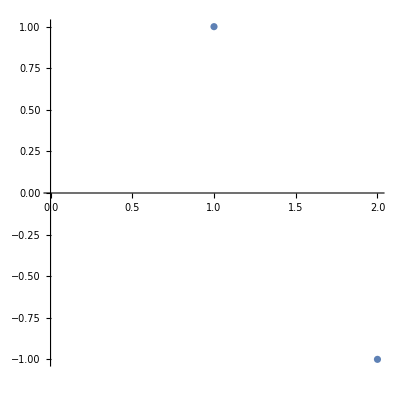

```mathematica
complexn[n_]:=Ceiling[n/8]*Cos[Mod[n,8]*Pi/4]+Ceiling[n/8]*I*Sin[Mod[n,8]*Pi/4]
ListPlot[complexn[ulamslist[8]],AspectRatio->1]
```

### Examples of ulamslist

```mathematica
ulamslist[3]
```

{3,10,5,16,8,4,2,1}

```mathematica
ulamslist[5]
```

{5,16,8,4,2,1}

```mathematica
ulamslist[7]
```

{7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

```mathematica
ulamslist[9]
```

{9,28,14,7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

```mathematica
ulamslist[10]
```

{10,5,16,8,4,2,1}

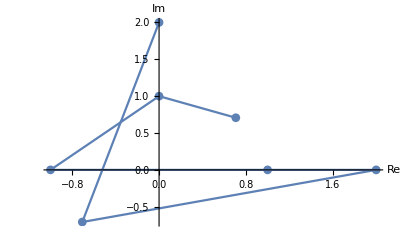

```mathematica
data=Transpose@{X,Y};
ListPlot[data,Joined->True,AxesLabel->{"Re","Im"},PlotMarkers->Automatic]
```

### The code giving the graphic form of ulams list in mod 8 format, ulamgraph.

```mathematica
datlist[n_]:=Transpose@{tablereal[n],tableimag[n]}
ulamgraph[n_]:=ListPlot[datlist[n],Joined->True,(*AxesLabel->{"Re","Im"},*)PlotMarkers->Automatic,PlotRange->{{Min[tablereal[n]],Max[tablereal[n]]},{Min[tableimag[n]],Max[tableimag[n]]}}, PlotRangeClipping->False]
```

### Examples of ulamgraph and ulamslist

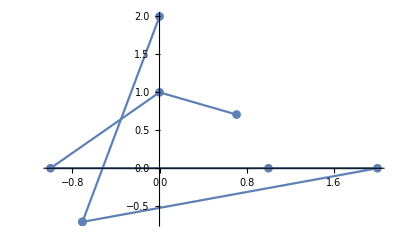

```mathematica
ulamgraph[10]
```

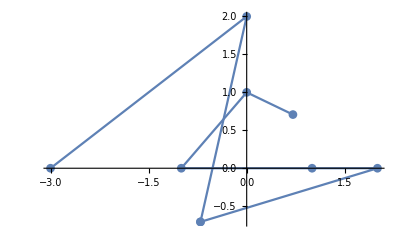

```mathematica
ulamgraph[20]
```

```mathematica
ulamslist[27]
```

{27,82,41,124,62,31,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

```mathematica
ulamslistmod8[27]
```

{3,2,1,4,6,7,6,7,6,7,6,3,2,1,4,2,1,4,6,3,2,1,4,6,7,6,3,2,1,4,6,7,6,7,6,3,2,1,4,2,5,0,4,6,7,6,3,2,1,4,6,3,2,1,4,6,7,6,7,6,7,6,7,6,3,2,5,0,4,6,7,6,7,6,3,2,5,0,0,4,2,1,4,2,1,4,2,5,0,0,4,2,5,0,4,6,7,6,3,2,5,0,0,0,4,2,5,0,0,4,2,1}

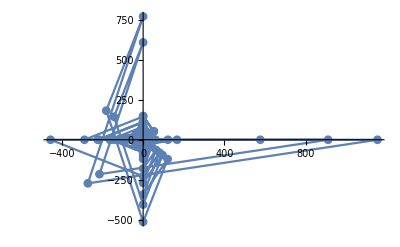

```mathematica
ulamgraph[27]
```

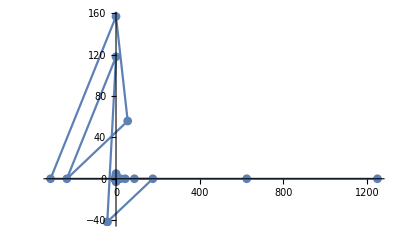

```mathematica
ulamgraph[10000]
```

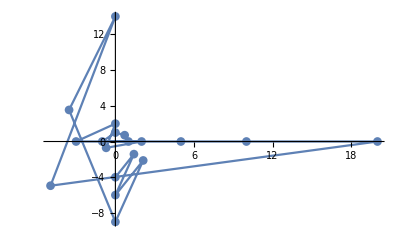

```mathematica
ulamgraph[30]
```

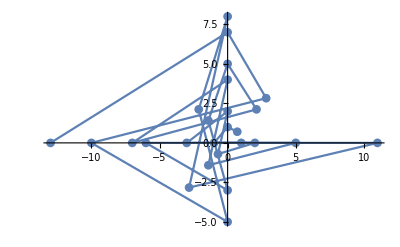

```mathematica
ulamgraph[100]
```

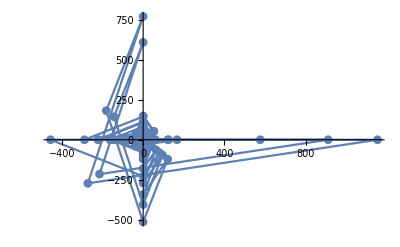

```mathematica
ulamgraph[1000]
```

```mathematica
ulamslist[1000]
```

{1000,500,250,125,376,188,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

```mathematica
ulamslist[27]
```

{27,82,41,124,62,31,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

{300,150,75,226,113,340,170,85,256,128,64,32,16,8,4,2,1}

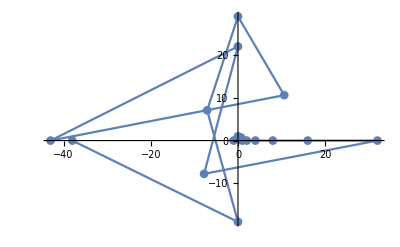

```mathematica
ulamslist[300]
ulamgraph[300]
```

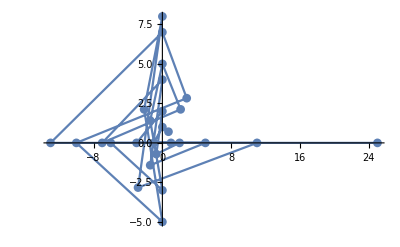

{200,100,50,25,76,38,19,58,29,88,44,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

-Graphics-

{27,82,41,124,62,31,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

```mathematica
ulamgraph[200]
ulamslist[200]
ulamgraph[27]
ulamslist[27]
```

### Alternative graphs and data export attempts

```mathematica
treeplt:=TreePlot[{3->10,6->3,12->6,10->5,20->10,5->16,16->8,8->4,4->2,2->1,20->40,13->40},VertexLabeling->True]
```

```mathematica
Export["treeplt.jpg",treeplt]
```

treeplt.jpg

```mathematica
Export[LocalObject["treeplt"],treeplt,"pdf"]
```

LocalObject[file:///C:/Users/Tyler/AppData/Roaming/Wolfram/Objects/treeplt]

```mathematica
Export[LocalObject["plot"],Plot[Sin[x],{x,0,10}],"PNG"]
```

LocalObject[file:///C:/Users/Tyler/AppData/Roaming/Wolfram/Objects/plot]